# FSAE Data Analysis

## Data Collection

### Functions

These will be used to do all the data manipulation on the incoming data.

```mathematica
condense[arr_,arr2_] :=
If[
arr == {},
{},
Module[{x = arr, y},x[[1;;Length[x],1]] = (*Quantity[x[[1;;Length[x],3]],"seconds"]*) x[[1;;Length[x],3]];y = x[[1;;Length[x],1;;2]];
y[[1;;Length[x],2]] =  (*Quantity[y[[1;;Length[x],2]],arr2]*) y[[1;;Length[x],2]];
y
]
]

getsensor[table_,name_,unit_] :=
Module[{x, y},
x = Select[table, #[[1,1]] == name &];If[x =={},{},condense[x[[1]],unit]]
]

filter[table_,cutoff_] :=
Module[{x=table,y},
y=LowpassFilter[x[[1;;Length[x],2]],cutoff];
x[[1;;Length[x],2]] = y;
If[x =={},{},x]
]

TwoAxisListPlot[{f_,g_}]:=Module[{fgraph,ggraph,frange,grange,fticks,gticks},{fgraph,ggraph}=MapIndexed[ListPlot[#,Axes->True,PlotStyle->ColorData[1][#2[[1]]]]&,{f,g}];{frange,grange}=Last[PlotRange/.AbsoluteOptions[#,PlotRange]]&/@{fgraph,ggraph};
fticks=Last[Ticks/.AbsoluteOptions[fgraph,Ticks]]/._RGBColor|_GrayLevel|_Hue:>ColorData[1][1];
gticks=(MapAt[Function[r,Rescale[r,grange,frange]],#,{1}]&/@Last[Ticks/.AbsoluteOptions[ggraph,Ticks]])/._RGBColor|_GrayLevel|_Hue->ColorData[1][2];
Show[fgraph,ggraph/.Graphics[graph_,s___]:>Graphics[GeometricTransformation[graph,RescalingTransform[{{0,1},grange},{{0,1},frange}]],s],Axes->False,Frame->True,FrameStyle->{ColorData[1]/@{1,2},{Automatic,Transparent}},FrameTicks->{{fticks,gticks},{Automatic,Automatic}}]]

TwoAxisListLinePlot[{f_,g_}]:=Module[{fgraph,ggraph,frange,grange,fticks,gticks},{fgraph,ggraph}=MapIndexed[ListLinePlot[#,Axes->True,PlotStyle->ColorData[1][#2[[1]]]]&,{f,g}];{frange,grange}=Last[PlotRange/.AbsoluteOptions[#,PlotRange]]&/@{fgraph,ggraph};
fticks=Last[Ticks/.AbsoluteOptions[fgraph,Ticks]]/._RGBColor|_GrayLevel|_Hue:>ColorData[1][1];
gticks=(MapAt[Function[r,Rescale[r,grange,frange]],#,{1}]&/@Last[Ticks/.AbsoluteOptions[ggraph,Ticks]])/._RGBColor|_GrayLevel|_Hue->ColorData[1][2];
Show[fgraph,ggraph/.Graphics[graph_,s___]:>Graphics[GeometricTransformation[graph,RescalingTransform[{{0,1},grange},{{0,1},frange}]],s],Axes->False,Frame->True,FrameStyle->{ColorData[1]/@{1,2},{Automatic,Transparent}},FrameTicks->{{fticks,gticks},{Automatic,Automatic}}]]

TwoAxisPlot[{f_,g_},{x_,x1_,x2_}]:=Module[{fgraph,ggraph,frange,grange,fticks,gticks},{fgraph,ggraph}=MapIndexed[Plot[#,{x,x1,x2},Axes->True,PlotStyle->ColorData[1][#2[[1]]]]&,{f,g}];{frange,grange}=(PlotRange/.AbsoluteOptions[#,PlotRange])[[2]]&/@{fgraph,ggraph};fticks=N@FindDivisions[frange,5];gticks=Quiet@Transpose@{fticks,ToString[NumberForm[#,2],StandardForm]&/@Rescale[fticks,frange,grange]};Show[fgraph,ggraph/.Graphics[graph_,s___]:>Graphics[GeometricTransformation[graph,RescalingTransform[{{0,1},grange},{{0,1},frange}]],s],Axes->False,Frame->True,FrameStyle->{ColorData[1]/@{1,2},{Automatic,Automatic}},FrameTicks->{{fticks,gticks},{Automatic,Automatic}}]]
```

### Import

This will take in the csv, sort it and then truncate the end to get rid of debugging info from previous data processing and to get rid of garbage data that will always be at the end of the data from the SD card

```mathematica
SetDirectory[NotebookDirectory[]];
infile = "2000.TXT";
outfile = "out.csv";
Run["Translate_CAN.exe " . infile . " " . outfile];

data = Import["out.csv"];
len = Length[data]-15;
data = data[[len - 1500000;;len]]; 
data = GatherBy[data, First];
```

Part::take: "Cannot take positions -1499993 through 7 in {{\"<Suspension Position FL>\", 6.9702, 992.567}, {\"<Suspension Position FR>\", 7.26317, 992.567}, {\"<Suspension Position FL>\", 6.9702, 992.568}, {\"<Suspension Position FR>\", 7.26317, 992.568}, {\"<Yaw Rate>\", 0.165, 992.568}, {\"<Lateral Acceleration>\", 0.0345254, 992.568}, {\"<Yaw Acceleration>\", 0.225, 992.568}, {\"<Longitudinal Acceleration>\", 0.0062426, 992.568}, {\"<Suspension Position FL>\", 6.95799, 992.569}, «34», {\"<Suspension Position FR>\", 7.27537, 992.582}, {\"<Yaw Rate>\", 0.215, 992.583}, {\"<Lateral Acceleration>\", 0.0329966, 992.583}, {\"<Yaw Acceleration>\", 0.3375, 992.583}, {\"<Longitudinal Acceleration>\", 0.003185, 992.583}, {\"<Suspension Position FL>\", 6.9702, 992.583}, {\"<Suspension Position FR>\", 7.25096, 992.583}, «2239533»}. (*ButtonBox[

GatherBy::list: List expected at position 1 in GatherBy[{{"Suspension Position FL", 6.9702, 992.567}, {"Suspension Position FR", 7.26317, 992.567}, {"Suspension Position FL", 6.9702, 992.568}, {"Suspension Position FR", 7.26317, 992.568}, {"Yaw Rate", 0.165, 992.568}, {"Lateral Acceleration", 0.0345254, 992.568}, {"Yaw Acceleration", 0.225, 992.568}, {"Longitudinal Acceleration", 0.0062426, 992.568}, {"Suspension Position FL", 6.95799, 992.569}, « 34 », {"Suspension Position FR", 7.27537, 992.582}, {"Yaw Rate", 0.215, 992.583}, {"Lateral Acceleration", 0.0329966, 992.583}, {"Yaw Acceleration", 0.3375, 992.583}, {"Longitudinal Acceleration", 0.003185, 992.583}, {"Suspension Position FL", 6.9702, 992.583}, {"Suspension Position FR", 7.25096, 992.583}, « 2239533 »} ⟦ -1499993 ;; 7 ⟧, First].

Part::take: Cannot take positions -1499993 through 7 in {{"Suspension Position FL", 6.9702, 992.567}, {"Suspension Position FR", 7.26317, 992.567}, {"Suspension Position FL", 6.9702, 992.568}, {"Suspension Position FR", 7.26317, 992.568}, {"Yaw Rate", 0.165, 992.568}, {"Lateral Acceleration", 0.0345254, 992.568}, {"Yaw Acceleration", 0.225, 992.568}, {"Longitudinal Acceleration", 0.0062426, 992.568}, {"Suspension Position FL", 6.95799, 992.569}, « 34 », {"Suspension Position FR", 7.27537, 992.582}, {"Yaw Rate", 0.215, 992.583}, {"Lateral Acceleration", 0.0329966, 992.583}, {"Yaw Acceleration", 0.3375, 992.583}, {"Longitudinal Acceleration", 0.003185, 992.583}, {"Suspension Position FL", 6.9702, 992.583}, {"Suspension Position FR", 7.25096, 992.583}, « 2239533 »}.

GatherBy::list: List expected at position 1 in GatherBy[{{"Suspension Position FL", 6.9702, 992.567}, {"Suspension Position FR", 7.26317, 992.567}, {"Suspension Position FL", 6.9702, 992.568}, {"Suspension Position FR", 7.26317, 992.568}, {"Yaw Rate", 0.165, 992.568}, {"Lateral Acceleration", 0.0345254, 992.568}, {"Yaw Acceleration", 0.225, 992.568}, {"Longitudinal Acceleration", 0.0062426, 992.568}, {"Suspension Position FL", 6.95799, 992.569}, « 34 », {"Suspension Position FR", 7.27537, 992.582}, {"Yaw Rate", 0.215, 992.583}, {"Lateral Acceleration", 0.0329966, 992.583}, {"Yaw Acceleration", 0.3375, 992.583}, {"Longitudinal Acceleration", 0.003185, 992.583}, {"Suspension Position FL", 6.9702, 992.583}, {"Suspension Position FR", 7.25096, 992.583}, « 2239533 »} ⟦ -1499993 ;; 7 ⟧, First].

### Setup Variables

Get all sensors put into a variable for ploting and what not. They are setup so that the first element of each entry contains the timestamp. Also, any extra data manipulation to get value into something meaningful is executed here.

Get Sensor Output Format:
{{t1,d1},{t2,d2},{t3,d3}, ...}
where t is time and d is the data value

```mathematica
spfl = getsensor[data, "Suspension Position FL", "Millimeters"];
spfr = getsensor[data, "Suspension Position FR","Millimeters"];
sprl = getsensor[data, "Suspension Position RL","Millimeters"];
sprr = getsensor[data, "Suspension Position RR","Millimeters"];
bp0 = getsensor[data, "Brake Pressure 0","PSI"];
bp1 = getsensor[data, "Brake Pressure 1","PSI"];
sta = getsensor[data, "Steering Angle","Degrees"];
ywr = getsensor[data, "Yaw Rate","Degrees reciprocal seconds"];
ywa = getsensor[data, "Yaw Acceleration","Degrees reciprocal seconds squared"];
lona = getsensor[data, "Longitudinal Acceleration","Earth's gravity"];
lata = getsensor[data, "Lateral Acceleration","Earth's gravity"];
ttfr1 = getsensor[data, "Tire Temperature FR Ch 1","Celcius"];
ttfr3 = getsensor[data, "Tire Temperature FR Ch 3","Celcius"];
ttfr6 = getsensor[data, "Tire Temperature FR Ch 6","Celcius"];
ttfr8 = getsensor[data, "Tire Temperature FR Ch 8","Celcius"];
ttfl1 = getsensor[data, "Tire Temperature FL Ch 1","Celcius"];
ttfl3 = getsensor[data, "Tire Temperature FL Ch 3","Celcius"];
ttfl6 = getsensor[data, "Tire Temperature FL Ch 6","Celcius"];
ttfl8 = getsensor[data, "Tire Temperature FL Ch 8","Celcius"];
ttrl1 = getsensor[data, "Tire Temperature RL Ch 1","Celcius"];
ttrl3 = getsensor[data, "Tire Temperature RL Ch 3","Celcius"];
ttrl6 = getsensor[data, "Tire Temperature RL Ch 6","Celcius"];
ttrl8 = getsensor[data, "Tire Temperature RL Ch 8","Celcius"];
ttrr1 = getsensor[data, "Tire Temperature RR Ch 1","Celcius"];
ttrr3 = getsensor[data, "Tire Temperature RR Ch 3","Celcius"];
ttrr6 = getsensor[data, "Tire Temperature RR Ch 6","Celcius"];
ttrr8 = getsensor[data, "Tire Temperature RR Ch 8","Celcius"];
rpm = getsensor[data, "RPM","RPM"];
tp = getsensor[data, "Throttle Position","Percent"];
map = getsensor[data, "Manifold Pressure","Kilopascals"];
bv = getsensor[data, "Battery Voltage","Volts"];
pw = getsensor[data, "Injector Pulse Width","Micro Seconds"];
ot = getsensor[data, "Oil Temperature","Celcius"];
op = getsensor[data, "Oil Pressure","PSI"];
et = getsensor[data, "Engine Temperature","Celcius"];
lm = getsensor[data, "Lambda","Lambda"];
wsfl = getsensor[data, "Wheel Speed FL","miles per hour"];
wsfr = getsensor[data, "Wheel Speed FR","miles per hour"];
wsrl = getsensor[data, "Wheel Speed RL","miles per hour"];
wsrr = getsensor[data, "Wheel Speed RR","miles per hour"];
gspd = getsensor[data, "Ground Speed","miles per hour"];

lata = MovingAverage[Map[Mean,Partition[lata,2]],25];
lona = MovingAverage[Map[Mean,Partition[lona,2]],25];
ywa = MovingAverage[Map[Mean,Partition[ywa,2]],25];
ywr = MovingAverage[Map[Mean,Partition[ywr,2]],25];
spfl = MovingAverage[Map[Mean,Partition[spfl,25]],20];
spfr = MovingAverage[Map[Mean,Partition[spfr,25]],20];
sprl = MovingAverage[Map[Mean,Partition[sprl,25]],20];
sprr = MovingAverage[Map[Mean,Partition[sprr,25]],20];
sta = MovingAverage[sta,15];
wsfl = MovingAverage[wsfl,15];
wsfr = MovingAverage[wsfr,15];
wsrl = MovingAverage[wsrl,15];
wsrr = MovingAverage[wsrr,15];
bp0 = MovingAverage[bp0,25];
bp1 = MovingAverage[bp1,25];
tp = MovingAverage[tp,25];
op = MovingAverage[op,25];
rpm = MovingAverage[rpm,25];
lm = MovingAverage[lm,15];
gspd = Transpose@{wsfl[[All,1]],(wsfl[[All,2]] + wsfr[[1;;Length[wsfl],2]]) / 2};
dspd = Transpose@{wsrl[[All,1]],(wsrl[[All,2]] + wsrr[[1;;Length[wsrl],2]]) / 2};
slip = Transpose@{dspd[[All,1]],Abs[(dspd[[All,2]] - gspd[[1;;Length[dspd],2]]) / gspd[[All,2]]]};
lata[[All,2]] = lata[[All,2]] - .04;
ywr[[All,2]] = ((ywr[[All,2]] - .26)/360)*2*3.14;
ywa[[All,2]] = (ywa[[All,2]]/360)*2*3.14;
gsum = Transpose@{lata[[1;;Length[lona],1]], Abs[lata[[1;;Length[lona],2]]] + Abs[lona[[All,2]]]};
sta[[All,2]] = (sta[[All,2]] / 360) * 2 * 3.14 - .69;
spfr[[All,2]]= spfr[[All,2]] - 19.1;
spfl[[All,2]]= spfl[[All,2]];
sprr[[All,2]]= sprr[[All,2]] - 11.5;
sprl[[All,2]]= sprl[[All,2]];

iop = Interpolation[op];
islip = Interpolation[slip];
ilona = Interpolation[lona];
ilata = Interpolation[lata];
```

MovingAverage::arg2: The second argument 20 must be a positive integer less than or equal to the length 0 of the first argument, or a vector of length less than or equal to the length of the first argument.

Part::partw: Part 2 of {} does not exist.

Set::partw: Part 2 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Set::partw: Part 2 of {} does not exist.

Interpolation::inddp: The point 1389.13 in dimension 1 is duplicated.

Interpolation::inddp: The point 1275.14 in dimension 1 is duplicated.

## Plot Data

### 2D vs Time

#### Oil Pressure under Acceleration

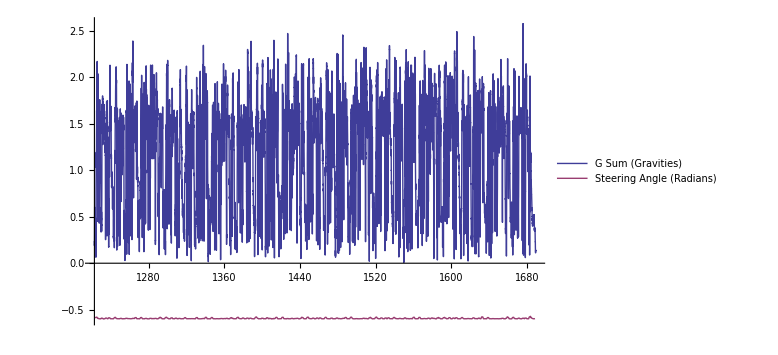

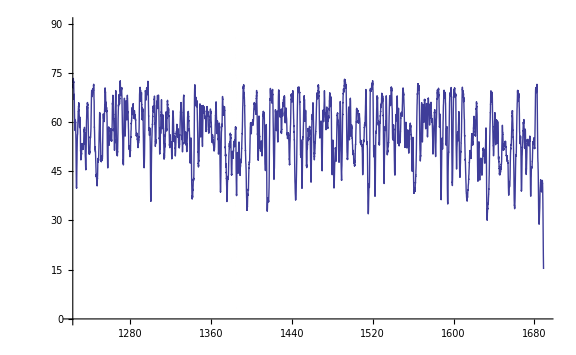

```mathematica
ListLinePlot[{gsum,sta}, AxesLabel->Automatic,PlotLegends->{"G Sum (Gravities)","Steering Angle (Radians)"}, PlotStyle->{Thick,Thick},ImageSize->Large]
ListLinePlot[op, PlotRange->{0,90}, PlotStyle->Thick,ImageSize->Large, PlotLegends-> "Oil Pressure (PSI)"]
```

#### RPM, Battery Voltage and Engine and Oil Temperature

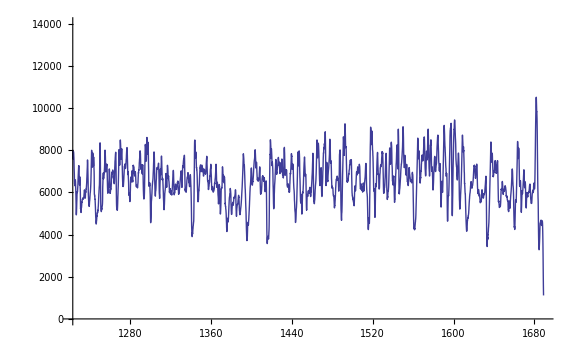

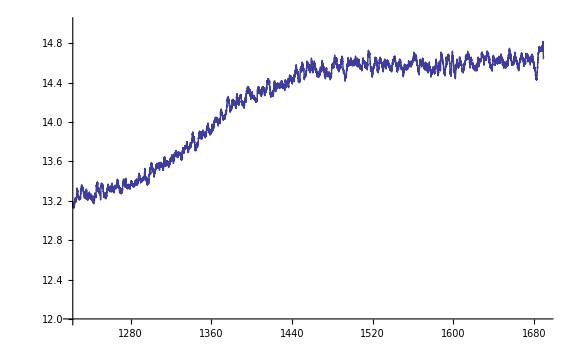

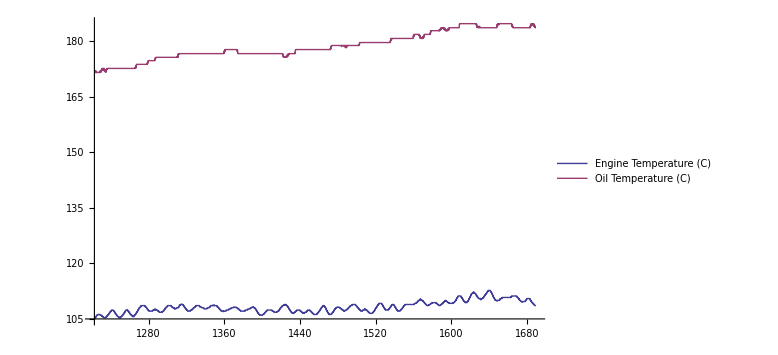

```mathematica
ListLinePlot[rpm, PlotRange->{0,14000},ImageSize->Large, PlotLegends->"RPM"]
ListLinePlot[bv,ImageSize->Large,PlotRange->{12,15}, PlotLegends->"Battery Voltage (V)"]
ListLinePlot[{et,ot},ImageSize->Large, PlotLegends->{"Engine Temperature (C)","Oil Temperature (C)"}]
```

#### Yaw Data

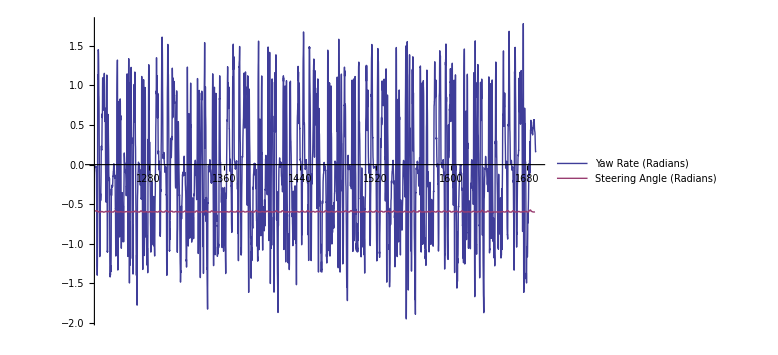

```mathematica
ListLinePlot[{ywr,sta}, ImageSize->Large,AxesLabel->Automatic,PlotStyle->Thick,PlotLegends->{ "Yaw Rate (Radians)","Steering Angle (Radians)"}]
```

#### Ground Speed with Brake Pressure, Throttle Position, Wheel Slip and Longitudinal Acceleration

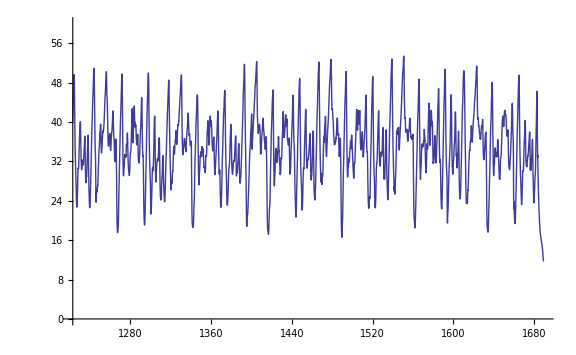

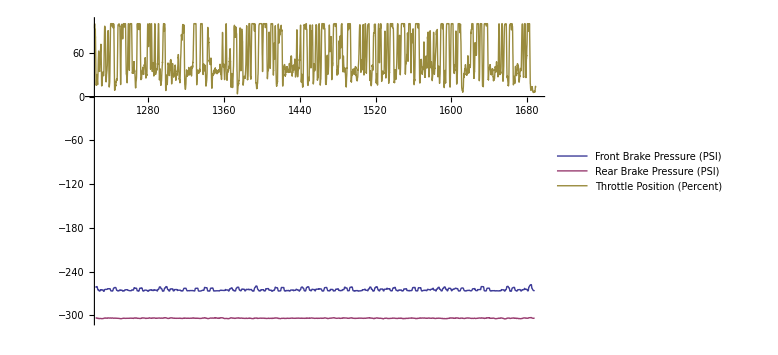

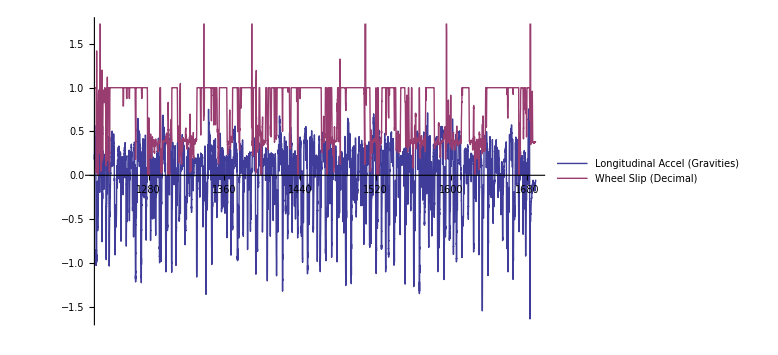

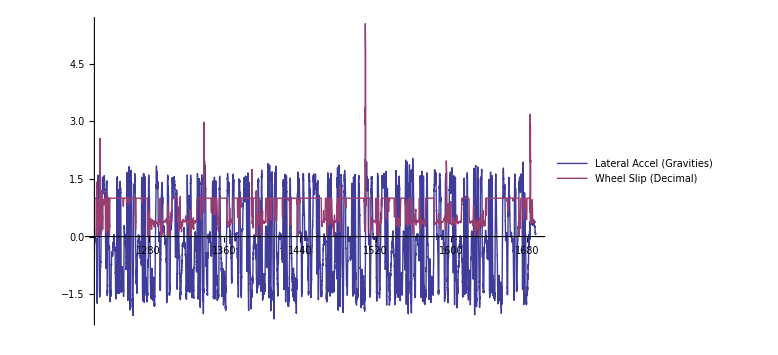

```mathematica
ListLinePlot[gspd, PlotLegends-> "Ground Speed (MPH)", ImageSize->Large,PlotStyle->Thick,PlotRange->{0,60}]
ListLinePlot[{bp0,bp1,tp}, PlotLegends->{"Front Brake Pressure (PSI)","Rear Brake Pressure (PSI)",  "Throttle Position (Percent)","Slip (Percent)"}, ImageSize->Large,PlotStyle->Thick]
ListLinePlot[{lona,slip}, PlotLegends-> {"Longitudinal Accel (Gravities)","Wheel Slip (Decimal)"}, ImageSize->Large,PlotStyle->Thick]
ListLinePlot[{lata,slip}, PlotLegends-> {"Lateral Accel (Gravities)","Wheel Slip (Decimal)"}, ImageSize->Large,PlotStyle->Thick]
```

#### Lateral and Longidutinal Accel - Wheel Slip Plot

#### Throttle Position and Lambda

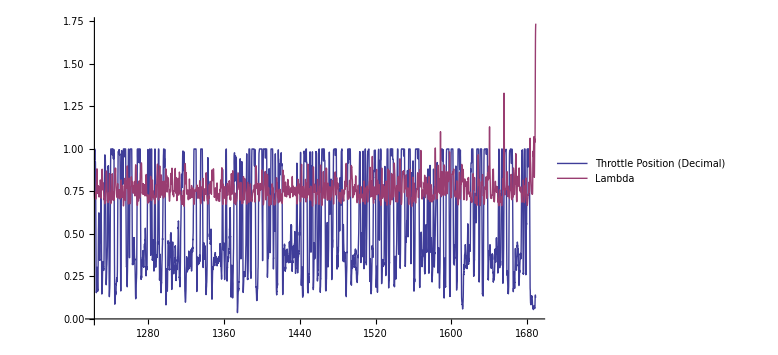

```mathematica
ListLinePlot[{Transpose@{tp[[All,1]],tp[[All,2]]/100},lm},PlotLegends->{"Throttle Position (Decimal)","Lambda"}, ImageSize->Large,PlotStyle->Thick]
```

### 2D Trend Plots

#### Throttle Position - Wheel Slip Plot

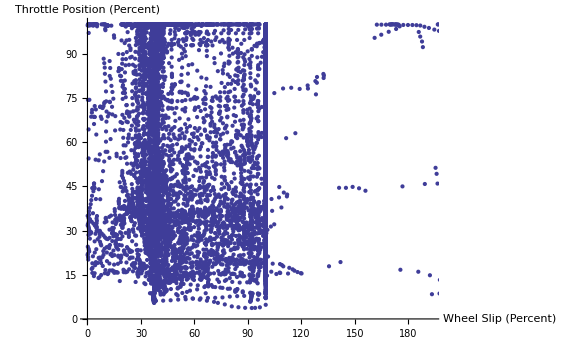

```mathematica
ListPlot[Transpose@{slip[[1;;Length[tp],2]]*100,tp[[All,2]]},ImageSize->Large,AxesLabel->{"Wheel Slip (Percent)","Throttle Position (Percent)"}]
```

#### RPM - Battery Voltage Plot

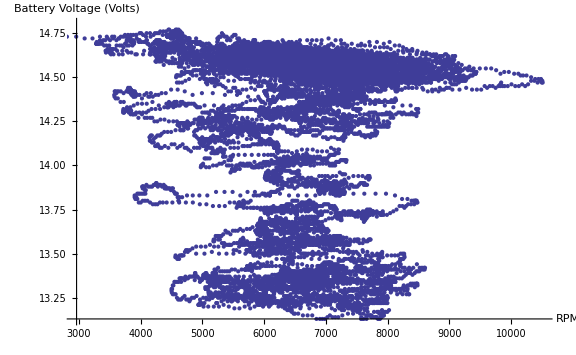

```mathematica
ListPlot[Transpose@{rpm[[All,2]],bv[[1;;Length[rpm],2]]},ImageSize->Large,AxesLabel->{"RPM","Battery Voltage (Volts)"}]
```

#### Oil Temperature - Egnine Temperature Plot

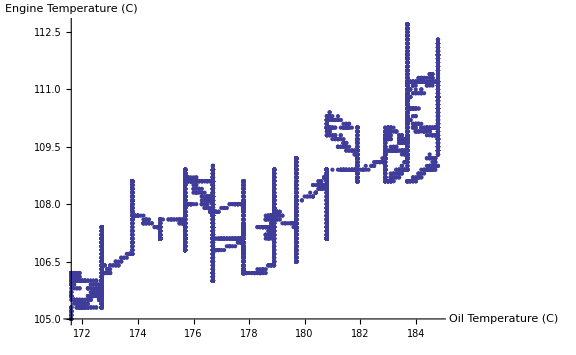

```mathematica
ListPlot[Transpose@{ot[[All,2]],et[[1;;Length[ot],2]]},ImageSize->Large,AxesLabel->{"Oil Temperature (C)","Engine Temperature (C)"}]
```

#### Oil Pressure - Oil Temperature Plot

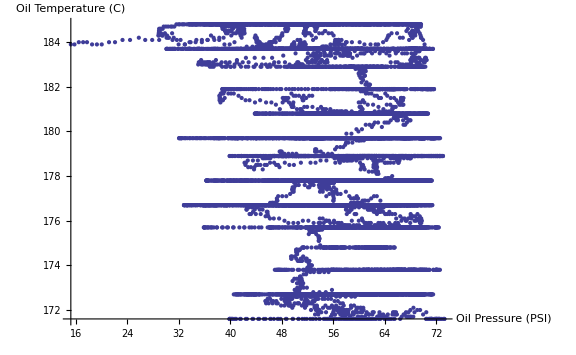

```mathematica
ListPlot[Transpose@{op[[All,2]],ot[[1;;Length[op],2]]},ImageSize->Large,AxesLabel->{"Oil Pressure (PSI)","Oil Temperature (C)"}]
```

#### G - G Plot

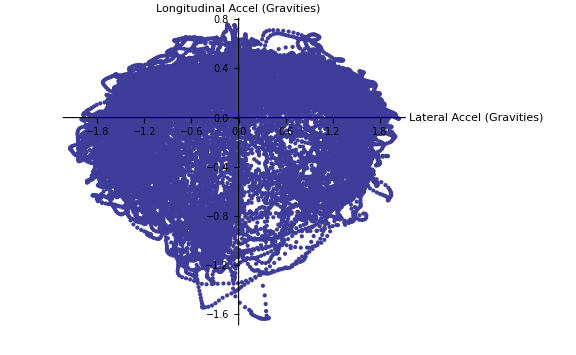

```mathematica
ListPlot[Transpose@{lata[[1;;Length[lona],2]],lona[[All,2]]},ImageSize->Large,AxesLabel->{"Lateral Accel (Gravities)","Longitudinal Accel (Gravities)"}]
```

#### Lambda - Throttle Position Plot

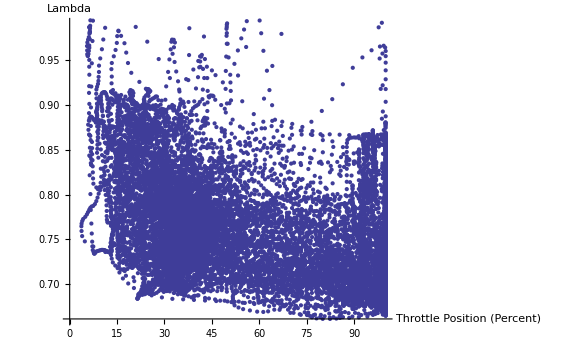

```mathematica
ListPlot[Transpose@{tp[[All,2]],lm[[1;;Length[tp],2]]},ImageSize->Large,AxesLabel->{"Throttle Position (Percent)","Lambda"}]
```